```mathematica
(*Protocols*)
Ωp[t_]:= Ω0*Exp[- (t-tf/2-t0)^2/σ^2]
Ωs[t_]:= Ω0*Exp[- (t-tf/2+t0)^2/σ^2]
ΩpTR[t_,a_]:= Ω0*Exp[-(f[t, a]-tforiginal/2-tforiginal/10)^2/(tforiginal/6)^2]*( a -(a-1)*Cos[2*Pi*a*t/tforiginal])
ΩsTR[t_,a_]:= Ω0*Exp[-(f[t, a]-tforiginal/2+tforiginal/10)^2/(tforiginal/6)^2]*( a -(a-1)*Cos[2*Pi*a*t/tforiginal])
dΩp[t_]:=D[Ωp[b],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_]:=2*(dΩp[t]*Ωs[t]-Ωp[t]*dΩs[t])/(Ωp[t]^2 + Ωs[t]^2)
tforiginal = 10
f[t_, a_]:= a*t - (tforiginal/(2*Pi*a))*(a-1)*Sin[2*Pi*a*t/tforiginal]
df[t_,a_]:= a -(a-1)*Cos[2*Pi*a*t/tforiginal]
(*Parameters*)
ℏ = 1
Δ = 0
ti = 0
Ω0 = 2*Pi*3 (*MHz*)
tf = 0.1 (*μs*)
t0 = tf/10 (*μs*)
σ = tf/6 (*μs*)
a = tforiginal/tf
θ[Ωp_,Ωs_]:= ArcTan[Ωp/Ωs]
(*Eigenstates and Hamiltonian*)
v[θ_] := {Cos[θ],0,- Sin[θ]}
vCD[Ωp_,Ωs_,Ωa_]:= {-Ωs/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2)),-(ⅈ Ωa)/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2)),Ωp/(√(Abs[Ωa]^2+Abs[Ωp]^2+Abs[Ωs]^2))}
H[Ωp_,Ωs_,Δ_] := (ℏ/2)*{{0,Ωp,0},{Ωp,2*Δ,Ωs},{0,Ωs,0}}
(*Solutions Schrödinger's equation*)
Sol = NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t]*c1[t]+(ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1,c2,c3},{t,ti,tf}]
SolCD = NDSolve[{ⅈ*ℏ*c1CD'[t] ==(ℏ/2)*Ωp[t]*c2CD[t]+ⅈ*(ℏ/2)*Ωa[t]*c3CD[t],ⅈ*ℏ*c2CD'[t] ==(ℏ/2)*Ωp[t]*c1CD[t]+(ℏ/2)*Ωs[t]*c3CD[t],ⅈ*ℏ*c3CD'[t] ==-ⅈ*(ℏ/2)*Ωa[t]*c1CD[t]+(ℏ/2)*Ωs[t]*c2CD[t],c1CD[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2CD[ti]==0,c3CD[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1CD,c2CD,c3CD},{t,ti,tf}]
SolTR= NDSolve[{ⅈ*ℏ*c1TR'[t] ==(ℏ/2)*ΩpTR[t,a]*c2TR[t],ⅈ*ℏ*c2TR'[t] ==(ℏ/2)*ΩpTR[t,a]*c1TR[t]+(ℏ/2)*ΩsTR[t,a]*c3TR[t],ⅈ*ℏ*c3TR'[t] ==(ℏ/2)*ΩsTR[t,a]*c2TR[t],c1TR[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ],c2TR[ti]==0,c3TR[ti]==-Ωp[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti]^2 ] },{c1TR,c2TR,c3TR},{t,ti,tf}]
(*Minimal fidelity?*)
(*Work quantum quench?*)
(*Mean energy? Zero*)
(*Fidelity with protocol time*)
```

```mathematica
ℏ = 1
Ωpi = 0.1
Ωpf = 10
ti = 0
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
Δ = 0.1
```

1

0.1

10

0

0.1

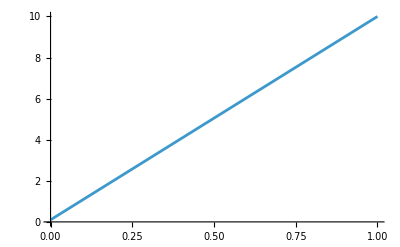

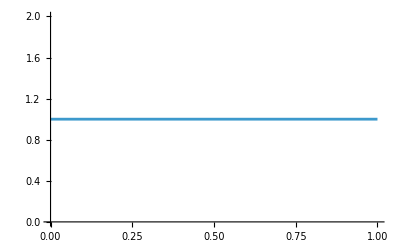

```mathematica
Plot[Ωp[t,1.0],{t,ti,1.0}]
Plot[Ωs[t],{t,ti,1.0}]
```

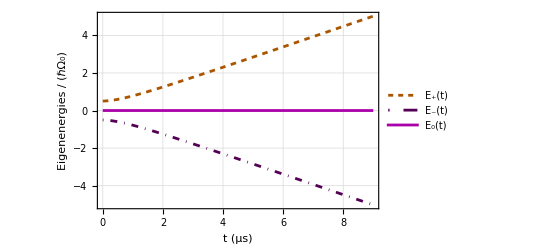

```mathematica
(*Autovalores*)
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Orange], Dashing[0.01]},FrameLabel ->{"t (μs)", "Eigenenergies / (ℏΩ_0)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Right,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2], {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Purple], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Right,0.86}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Magenta],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Right,0.78}]]]
```

```mathematica
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

{0.0454959,5.09554,10.1456,15.1956,20.2457,25.2957,30.3458,35.3958,40.4459,45.4959}

```mathematica
Δ= 0.1
tf = 9.0
Tmin = 0.1
Tmax = 100
m = 9
ΔT = (Tmax-Tmin)/m
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ/2)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

0.1

9.

0.1

100

9

11.1

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

```mathematica
Part[Sol,2]
```

{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}

```mathematica
(*Probabilities |1 >*)
p1 = Table[Abs[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p2 = Table[Abs[c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p3 = Table[Abs[c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929907,0.372193,0.204554,0.00211636,0.0219079,0.10104,0.104504,0.0446412,0.0213702,0.0251801}

{0.0593618,0.112802,0.224921,0.24218,0.151785,0.0424904,0.000391703,0.0229252,0.0488444,0.0390973}

{0.0107307,0.515003,0.570525,0.755704,0.826308,0.85647,0.895105,0.932435,0.929787,0.935724}

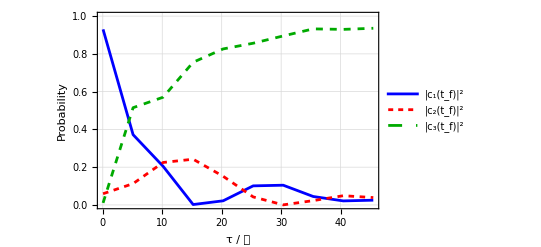

```mathematica
Show[ListPlot[Transpose[{time,p1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,p2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,p3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

```mathematica
ψ[t_]:= {{Evaluate[c1[t]/.Part[Flatten[Sol],1]]},{Evaluate[c2[t]/.Part[Flatten[Sol],2]]},{Evaluate[c3[t]/.Part[Flatten[Sol],3]]}}
```

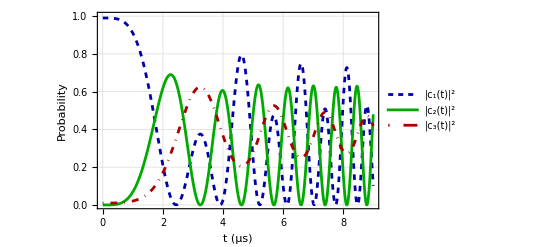

```mathematica
Show[Plot[Abs[Evaluate[c1[t]/.Part[Flatten[Sol],1]]]^2, {t,ti,tf},PlotRange->{0,1},PlotStyle->{Darker[Blue],Dashing[0.01]},PlotTheme-> "Detailed",FrameLabel ->{"t (μs)", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t)|^2",10]},LegendLayout->"Row"],{Right,0.32}]],
Plot[Abs[Evaluate[c2[t]/.Part[Flatten[Sol],2]]]^2, {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Green]},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t)|^2",10]},LegendLayout->"Row"],{Right,0.24}]],
Plot[Abs[Evaluate[c3[t]/.Part[Flatten[Sol],3]]]^2, {t,ti,tf},PlotTheme-> "Detailed",PlotStyle->{Darker[Red], DotDashed},FrameLabel ->{"t", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t)|^2",10]},LegendLayout->"Row"],{Right,0.16}]]]
```

```mathematica
Abs[Evaluate[c3[t]/.Part[Flatten[Sol],3]]]^2/.t->tf
```

0.418356